```mathematica
模拟大气中光的折射
```

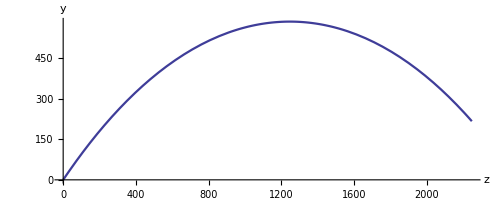

```mathematica
Clear[y,s,z]
tm=2.5*10^3;n[y_]:=2-10^-3*y;
equ={D[n[y[s]]*y'[s],s]==-10^-3,
D[n[y[s]]*z'[s],s]==0,
y[0]==0,y'[0]==Sin[π/4],
z[0]==0,z'[0]==Cos[π/4]};
sol=NDSolve[equ,{z,y},{s,0,tm}];
ParametricPlot[{z[s],y[s]}/.sol[[1]],
{s,0,tm},AxesLabel->{"z","y"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[n,equ,sol,tm]
```